```mathematica
ToInSymbol2[s_]:=SetsToSymbol[SymbolToSets[s],"T"]
```

```mathematica
CalculateInOutFormulaBorder[g_,border_,in_,out_]:=Block[{
currentEdge, 
edges, 
pos,
isInOut, gContract, gRemove, gIn, gOut, result, resIn, resOut, resContract, resRemove, repVertex},
edges=EdgeList[g];
For[pos=1,pos <=Length[edges],pos++,
currentEdge=edges[[pos]];
isInOut=MemberQ[in,currentEdge[[1]]]&&MemberQ[border,currentEdge[[2]]];
If[!isInOut,
isInOut=MemberQ[in,currentEdge[[2]]]&&MemberQ[border,currentEdge[[1]]];
currentEdge=UndirectedEdge[currentEdge[[2]],currentEdge[[1]]]
];
If[isInOut,
gContract=GContract[g,currentEdge];
repVertex={currentEdge[[1]]->currentEdge[[2]]};
gContract=Graph[VertexList[gContract]/.repVertex,Map[#[[1]]<->#[[2]]/.repVertex&,EdgeList[gContract]]];
gRemove=EdgeDelete[g,currentEdge];
resContract=CalculateInOutFormulaBorder[gContract,border,DeleteCases[in,currentEdge[[1]]],out];
resRemove=CalculateInOutFormulaBorder[gRemove,border,in,out];
(*Print[currentEdge->{Graph[gRemove,VertexLabels->"Name", ImageSize->50,GraphLayout->"TutteEmbedding"],resRemove,Graph[gContract,VertexLabels->"Name", ImageSize->50,GraphLayout->"TutteEmbedding"],resContract}];*)
result=resRemove-resContract;
Return[result]
];
];
gIn=Subgraph[g,in];
gOut=Subgraph[g,Join[border,out]];
resIn=If[VertexCount[gIn]==0,1,Fold [Plus,Map[ToInSymbol2,FindFullFormula[gIn]]]];
resOut=CalculateInOutFormulaFull[gOut,out,border];
(*Print[{Graph[gIn,VertexLabels->"Name", ImageSize->50,GraphLayout->"TutteEmbedding"],resIn,Graph[gOut,VertexLabels->"Name", ImageSize->50,GraphLayout->"TutteEmbedding"], resOut,resIn*resOut}];*)
Return[resIn*resOut]
]
```

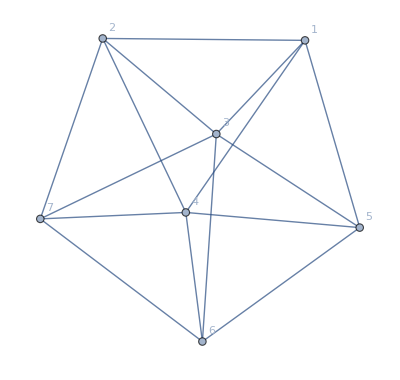

```mathematica
g=Graph[JacobsThalGraph[3],VertexLabels->"Name"]
```

```mathematica
MyRewrite5[CalculateInOutFormulaBorder[g,{1,2,7,6,5},{3},{4}]]
```

(-4+I4) O16x2x5x7 (-4+T3)+(-4+I4) O17x2x5x6 (-4+T3)+(-4+I4) O1x25x6x7 (-4+T3)+(-4+I4) O1x26x5x7 (-4+T3)+(-4+I4) O1x2x57x6 (-4+T3)+(-3+I4) O16x25x7 (-3+T3)+(-3+I4) O16x2x57 (-3+T3)+(-3+I4) O17x25x6 (-3+T3)+(-3+I4) O17x26x5 (-3+T3)+(-3+I4) O1x26x57 (-3+T3)

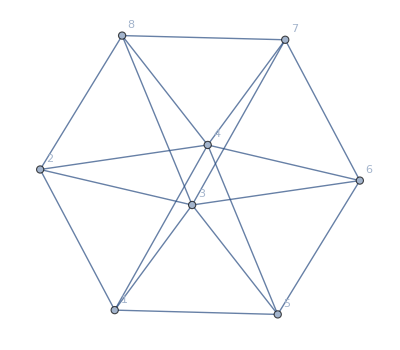

```mathematica
g2=Graph[JacobsThalGraph[4],VertexLabels->"Name"]
```

```mathematica
MyRewrite8[form_]:=Block[{vars=Select[DeleteDuplicates[ListofVars[form]],StringStartsQ[ SymbolName[#],"I"]&]},
If[vars=={},
Factor[form],
Total[
Table[
Total[Map[v*Factor[#]&,CoefficientList[form,v]]],
{v,vars}
]
]
]
]
```

```mathematica
MyRewrite9[form_]:=Block[{vars=Select[DeleteDuplicates[ListofVars[form]],StringStartsQ[ SymbolName[#],"O"]&]},
If[vars=={},
Factor[form],
Total[
Table[
Total[Map[v*MyRewrite8[Factor[#]]&,CoefficientList[form,v]]],
{v,vars}
]
]
]
]
```

```mathematica
MyRewrite10[form_]:=Block[{vars=Select[DeleteDuplicates[ListofVars[form]],StringStartsQ[ SymbolName[#],"T"]&]},
If[vars=={},
Factor[form],
Total[
Table[
Total[Map[v*Factor[#]&,CoefficientList[form,v]]],
{v,vars}
]
]
]
]
```

```mathematica
MyRewrite11[form_]:=Block[{vars=Select[DeleteDuplicates[ListofVars[form]],StringStartsQ[ SymbolName[#],"O"]&]},
If[vars=={},
Factor[form],
Total[
Table[
Total[Map[v*MyRewrite10[Factor[#]]&,CoefficientList[form,v]]],
{v,vars}
]
]
]
]
```

```mathematica
formg=CalculateInOutFormulaBorder[g,{3,4,5,8},{6,7},{1,2}]
```

18 O34x5+84 O3x4x5-14 I1 O3x4x5+5 I1x2 O3x4x5-19 I2 O3x4x5-5 I1 (O34x5+O3x4x5)+4 I1x2 (O34x5+O3x4x5)-8 I2 (O34x5+O3x4x5)-(9 O3x4x5-2 I1 O3x4x5+I1x2 O3x4x5-3 I2 O3x4x5) T6-(4 O34x5+9 O3x4x5-I1 O3x4x5-I2 O3x4x5-I1 (O34x5+O3x4x5)+I1x2 (O34x5+O3x4x5)-2 I2 (O34x5+O3x4x5)) T6+(4 O34x5+9 O3x4x5-I1 O3x4x5-I2 O3x4x5-I1 (O34x5+O3x4x5)+I1x2 (O34x5+O3x4x5)-2 I2 (O34x5+O3x4x5)) T6x7-(9 O3x4x5-2 I1 O3x4x5+I1x2 O3x4x5-3 I2 O3x4x5) T7-2 (4 O34x5+9 O3x4x5-I1 O3x4x5-I2 O3x4x5-I1 (O34x5+O3x4x5)+I1x2 (O34x5+O3x4x5)-2 I2 (O34x5+O3x4x5)) T7

```mathematica
Expand[formg]
```

18 O34x5-5 I1 O34x5+4 I1x2 O34x5-8 I2 O34x5+84 O3x4x5-19 I1 O3x4x5+9 I1x2 O3x4x5-27 I2 O3x4x5-4 O34x5 T6+I1 O34x5 T6-I1x2 O34x5 T6+2 I2 O34x5 T6-18 O3x4x5 T6+4 I1 O3x4x5 T6-2 I1x2 O3x4x5 T6+6 I2 O3x4x5 T6+4 O34x5 T6x7-I1 O34x5 T6x7+I1x2 O34x5 T6x7-2 I2 O34x5 T6x7+9 O3x4x5 T6x7-2 I1 O3x4x5 T6x7+I1x2 O3x4x5 T6x7-3 I2 O3x4x5 T6x7-8 O34x5 T7+2 I1 O34x5 T7-2 I1x2 O34x5 T7+4 I2 O34x5 T7-27 O3x4x5 T7+6 I1 O3x4x5 T7-3 I1x2 O3x4x5 T7+9 I2 O3x4x5 T7

```mathematica
ListofVars[formg]//DeleteDuplicates
```

{O34x5,O3x4x5,I1,I1x2,I2,T6,T7,T6x7}

```mathematica
repPoly=Map[#->Product[(x-i),{i,0,SymbolLevel[#]-1}]&,ListofVars[formg]//DeleteDuplicates]
```

{O34x5→(-1+x) x,O3x4x5→(-2+x) (-1+x) x,I1→x,I1x2→(-1+x) x,I2→x,T6→x,T7→x,T6x7→(-1+x) x}

```mathematica
Expand[formg/.repPoly]
```

150 x-419 x^2+462 x^3-263 x^4+83 x^5-14 x^6+x^7

```mathematica
ChromaticPolynomial[g,x]
```

210 x-565 x^2+594 x^3-320 x^4+95 x^5-15 x^6+x^7

```mathematica
MyRewrite9[CalculateInOutFormulaBorder[g,{3,4,5,8},{6,7},{1,2}]]
```

O3x4x5 (I1 O34x5 (-5+T6-T6x7+2 T7)-I1x2 O34x5 (-4+T6-T6x7+2 T7)+2 I2 O34x5 (-4+T6-T6x7+2 T7)+I2 O34x5 (18-5 I1+4 I1x2-4 T6+I1 T6-I1x2 T6+4 T6x7-I1 T6x7+I1x2 T6x7-8 T7+2 I1 T7-2 I1x2 T7)-I1 O34x5 (-18-4 I1x2+8 I2+4 T6+I1x2 T6-2 I2 T6-4 T6x7-I1x2 T6x7+2 I2 T6x7+8 T7+2 I1x2 T7-4 I2 T7)+I1x2 O34x5 (18-5 I1-8 I2-4 T6+I1 T6+2 I2 T6+4 T6x7-I1 T6x7-2 I2 T6x7-8 T7+2 I1 T7+4 I2 T7))+O34x5 (I1x2 (4-T6+T6x7-2 T7)+I1 (-5+T6-T6x7+2 T7)+2 I2 (-4+T6-T6x7+2 T7)+I2 (18-5 I1+4 I1x2-4 T6+I1 T6-I1x2 T6+4 T6x7-I1 T6x7+I1x2 T6x7-8 T7+2 I1 T7-2 I1x2 T7)+I1x2 (18-5 I1-8 I2-4 T6+I1 T6+2 I2 T6+4 T6x7-I1 T6x7-2 I2 T6x7-8 T7+2 I1 T7+4 I2 T7)+I1 (18+4 I1x2-8 I2-4 T6-I1x2 T6+2 I2 T6+4 T6x7+I1x2 T6x7-2 I2 T6x7-8 T7-2 I1x2 T7+4 I2 T7))+O34x5 (-I1x2 O3x4x5 (-9+2 T6-T6x7+3 T7)+3 I2 O3x4x5 (-9+2 T6-T6x7+3 T7)+I1 O3x4x5 (-19+4 T6-2 T6x7+6 T7)+I2 O3x4x5 (84-19 I1+9 I1x2-18 T6+4 I1 T6-2 I1x2 T6+9 T6x7-2 I1 T6x7+I1x2 T6x7-27 T7+6 I1 T7-3 I1x2 T7)-I1 O3x4x5 (-84-9 I1x2+27 I2+18 T6+2 I1x2 T6-6 I2 T6-9 T6x7-I1x2 T6x7+3 I2 T6x7+27 T7+3 I1x2 T7-9 I2 T7)+I1x2 O3x4x5 (84-19 I1-27 I2-18 T6+4 I1 T6+6 I2 T6+9 T6x7-2 I1 T6x7-3 I2 T6x7-27 T7+6 I1 T7+9 I2 T7))+O3x4x5 (I1x2 (9-2 T6+T6x7-3 T7)+3 I2 (-9+2 T6-T6x7+3 T7)+I1 (-19+4 T6-2 T6x7+6 T7)+I2 (84-19 I1+9 I1x2-18 T6+4 I1 T6-2 I1x2 T6+9 T6x7-2 I1 T6x7+I1x2 T6x7-27 T7+6 I1 T7-3 I1x2 T7)+I1x2 (84-19 I1-27 I2-18 T6+4 I1 T6+6 I2 T6+9 T6x7-2 I1 T6x7-3 I2 T6x7-27 T7+6 I1 T7+9 I2 T7)+I1 (84+9 I1x2-27 I2-18 T6-2 I1x2 T6+6 I2 T6+9 T6x7+I1x2 T6x7-3 I2 T6x7-27 T7-3 I1x2 T7+9 I2 T7))

```mathematica
MyRewrite11[CalculateInOutFormulaBorder[g,{3,4,5,8},{6,7},{1,2}]]
```

O3x4x5 ((-4+I1-I1x2+2 I2) O34x5 T6-(-4+I1-I1x2+2 I2) O34x5 T6x7+2 (-4+I1-I1x2+2 I2) O34x5 T7+O34x5 (18-5 I1+4 I1x2-8 I2-4 T6+I1 T6-I1x2 T6+2 I2 T6+4 T6x7-I1 T6x7+I1x2 T6x7-2 I2 T6x7) T7-O34x5 T6 (-18+5 I1-4 I1x2+8 I2-4 T6x7+I1 T6x7-I1x2 T6x7+2 I2 T6x7+8 T7-2 I1 T7+2 I1x2 T7-4 I2 T7)+O34x5 T6x7 (18-5 I1+4 I1x2-8 I2-4 T6+I1 T6-I1x2 T6+2 I2 T6-8 T7+2 I1 T7-2 I1x2 T7+4 I2 T7))+O34x5 ((-4+I1-I1x2+2 I2) T6+(4-I1+I1x2-2 I2) T6x7+2 (-4+I1-I1x2+2 I2) T7+(18-5 I1+4 I1x2-8 I2-4 T6+I1 T6-I1x2 T6+2 I2 T6+4 T6x7-I1 T6x7+I1x2 T6x7-2 I2 T6x7) T7+T6x7 (18-5 I1+4 I1x2-8 I2-4 T6+I1 T6-I1x2 T6+2 I2 T6-8 T7+2 I1 T7-2 I1x2 T7+4 I2 T7)+T6 (18-5 I1+4 I1x2-8 I2+4 T6x7-I1 T6x7+I1x2 T6x7-2 I2 T6x7-8 T7+2 I1 T7-2 I1x2 T7+4 I2 T7))+O34x5 (2 (-9+2 I1-I1x2+3 I2) O3x4x5 T6-(-9+2 I1-I1x2+3 I2) O3x4x5 T6x7+3 (-9+2 I1-I1x2+3 I2) O3x4x5 T7+O3x4x5 (84-19 I1+9 I1x2-27 I2-18 T6+4 I1 T6-2 I1x2 T6+6 I2 T6+9 T6x7-2 I1 T6x7+I1x2 T6x7-3 I2 T6x7) T7-O3x4x5 T6 (-84+19 I1-9 I1x2+27 I2-9 T6x7+2 I1 T6x7-I1x2 T6x7+3 I2 T6x7+27 T7-6 I1 T7+3 I1x2 T7-9 I2 T7)+O3x4x5 T6x7 (84-19 I1+9 I1x2-27 I2-18 T6+4 I1 T6-2 I1x2 T6+6 I2 T6-27 T7+6 I1 T7-3 I1x2 T7+9 I2 T7))+O3x4x5 (2 (-9+2 I1-I1x2+3 I2) T6+(9-2 I1+I1x2-3 I2) T6x7+3 (-9+2 I1-I1x2+3 I2) T7+(84-19 I1+9 I1x2-27 I2-18 T6+4 I1 T6-2 I1x2 T6+6 I2 T6+9 T6x7-2 I1 T6x7+I1x2 T6x7-3 I2 T6x7) T7+T6x7 (84-19 I1+9 I1x2-27 I2-18 T6+4 I1 T6-2 I1x2 T6+6 I2 T6-27 T7+6 I1 T7-3 I1x2 T7+9 I2 T7)+T6 (84-19 I1+9 I1x2-27 I2+9 T6x7-2 I1 T6x7+I1x2 T6x7-3 I2 T6x7-27 T7+6 I1 T7-3 I1x2 T7+9 I2 T7))

```mathematica
Expand[O34x5 (I1x2 (4-T6+T6x7-2 T7)+I1 (-5+T6-T6x7+2 T7)+2 I2 (-4+T6-T6x7+2 T7))+O3x4x5 (I1x2 (9-2 T6+T6x7-3 T7)+3 I2 (-9+2 T6-T6x7+3 T7)+I1 (-19+4 T6-2 T6x7+6 T7))]
```

-5 I1 O34x5+4 I1x2 O34x5-8 I2 O34x5-19 I1 O3x4x5+9 I1x2 O3x4x5-27 I2 O3x4x5+I1 O34x5 T6-I1x2 O34x5 T6+2 I2 O34x5 T6+4 I1 O3x4x5 T6-2 I1x2 O3x4x5 T6+6 I2 O3x4x5 T6-I1 O34x5 T6x7+I1x2 O34x5 T6x7-2 I2 O34x5 T6x7-2 I1 O3x4x5 T6x7+I1x2 O3x4x5 T6x7-3 I2 O3x4x5 T6x7+2 I1 O34x5 T7-2 I1x2 O34x5 T7+4 I2 O34x5 T7+6 I1 O3x4x5 T7-3 I1x2 O3x4x5 T7+9 I2 O3x4x5 T7